# Nyquist-Shannon Sampling Theorem

The Nyquist-Shannon Sampling theorem is a fundamental one providing the condition on the sampling frequency of a band-width limited continuous-time signal in order to be able to reconstruct it perfectly from its discrete-time (sampled) version. It stated that the sampling frequency must be at least two times the highest frequency of the continuous-time signal spectrum.

Set up of the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

## What is a Signal?

A signal is a time/space varying function which includes some useful information. Most of signals are continuous-time ones and hence can not be either stored (or transmitted) over realistic limited data storage (or band-limited propagation space) due to infinity of points to be processed.
Such signals could be of different sources or types, such as audio ones, or any real life physical measure or parameter retrieved by sensors (temp, humidity, speed, ...).

Example of a continuous-time* signal - Mean Temperature during 2016 in Rabat, Morocco:

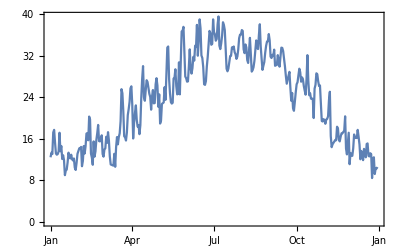

```mathematica
weatherData=WeatherData[{33.9716,6.8498}, "MeanTemperature", {{2016, 1, 1}, {2016, 12, 31}, "Day"}];
DateListPlot[weatherData,Joined -> True]
```

In order, to process real life signals either to store or transmit, we need to a sampling process them, making them discrete-time signal.

## Sampling Theorem

Sampling a continuous-time signal is getting one sample each sampling period T_s[s] , which means a sampling frequency equivalent to f_s=1/T_s[Hz].
The mean important decision to make is the sampling frequency value of f_s: Indeed, if its value is too big, we’ll get f_s samples per second, so large storage or large band width in order to transmit the data. If on the other hand, the value is too small, we won’t be able to reconstruct the signal from the samples.
Hence, there is a tradeoff to make in order to minimise the needed resources (storage or frequency band-width) while being able to reproduce the original signal from the samples.

One theorem provides an answer to this question, it’s the Nyquist-Shannon Sampling Theorem which states:

A continuous-time signal x(t) can be sampled at a frequency f_s in order to get a discrete-time copy of it x[n], and afterwards be reconstructed perfectly to its original form x(t) if f_s>2 f_max with f_max is the maximum frequency value of the x(t) signal spectrum

Next, we’ll consider a Sinc^2 function and see what happen to the sampled signal on the frequency domain using Fourier Transform

## Sampling Process

### Time Domain Analysis

Consider the function x(t)=Sinc^2(t) which represent a continuous-time signal.

Plot of the signal x(t)=Sinc^2(t):

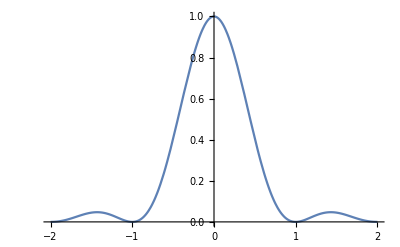

```mathematica
x[t_]:=(Sinc[Pi*t])^2;
Plot[x[t],{t,-2,2}]
```

Consider a sampling frequency f_sand let see what happen for different values of f_s.

Plot of the continuous-time and discrete-time (sampled) signals:

```mathematica
Manipulate[
Show[DiscretePlot[x[t],{t, -3, 3,1/fs},PlotRange->{{-3,3},{-0.1,1.1}},PerformanceGoal->"Quality",PlotStyle->Directive[Orange,Thick],PlotMarkers->Automatic],Plot[x[t],{t,-3,3}]],{{fs,15.25,"Frequency f_s"}, 0.5, 30,Appearance->"Labeled"}]
```

As we can see, for high values of f_s we can at least recognize visually the original continuous-time form on the x(t) signal. However, for small values of f_s such as f_s=0.1hz for instance, we can no more visually retrieve the form of the original Sinc^2 function, with only four sample over the 20 interval duration it’s quite impossible to go back from samples to continuous signal. Indeed, in such case, we are sure not satisfying the Nyquist-Shannon sampling condition.
In the time domain, we can somehow visually understand what’s happening, however, the theorem is more understandable when analyzed on the frequency domain.

### Frequency Domain

The spectrum analysis of signal x(t) allows us to understand easily and even prove the theorem ourselves.

TF[Sinc^2(a t)] = 1/(|a|)tri(f/a)

Fourier Transform of the signal x(t):

```mathematica
Simplify[FourierTransform[x[t],t,ω]]
```

(-2 ω Sign[ω]+(-2 π+ω) Sign[-2 π+ω]+(2 π+ω) Sign[2 π+ω])/(4 √2 π^(3/2))

Spectrum of the signal x(t)

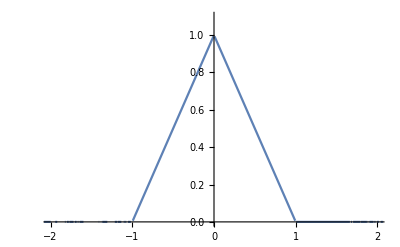

```mathematica
Plot[Sqrt[2*Pi]*FourierTransform[x[t],t,ω*2*Pi],{ω,-10,10},PlotRange->{{-2,2},{0,1.1}}]
```

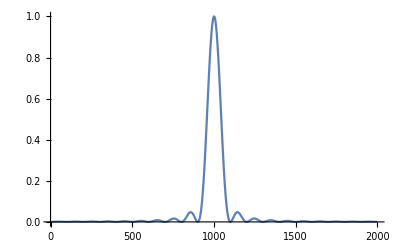

```mathematica
fs=100;
xn=Table[N[x[n/fs]],{n,-10*fs,10*fs}];
ListLinePlot[xn,PlotRange->All]
```

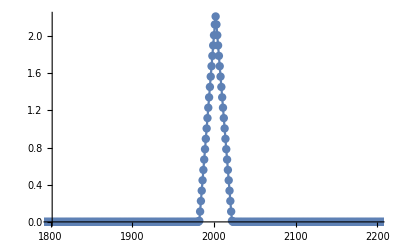

```mathematica
Xk =Abs[Fourier[xn]];
Xp =Join@@Table[Xk,3];
ListLinePlot[Xp,PlotRange->{{1800,2200},All},Mesh->All]
```

* The signal look continuous on the plot but any signal processed (transmitted, displayed, transmitted) is always a sampled version of the original continuous time parameter

## Reconstruction Process

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Ghassane Aniba

22 June 2017

ghassane@emi.ac.ma